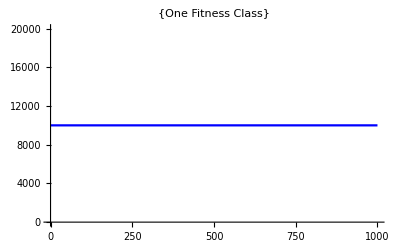

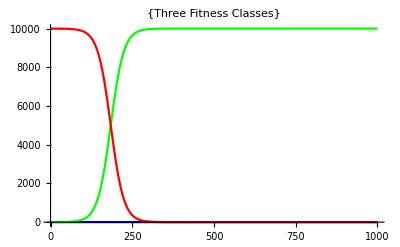

```mathematica
(* Testing SystemSolver, SolveDiffEqs *)
{Δc1,Δc2,popsize,timestep}={0.01,0.06,10^4,1000}; 
(* Testing system solver for one fitness class *)
genotypes={{1,1}};
genotypeabundances={10^4};
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
Plot[{n1[t]/.sol[[1]]},{t,0,timestep},PlotStyle->{Blue},PlotLabel->{"One Fitness Class"}]
(* Testing system solver for three fitness class *)
genotypes={{1,1},{1,2},{2,1}};
genotypeabundances={1,1,1 10^4-2};
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
Plot[{n1[t]/.sol[[1]],n2[t]/.sol[[1]],n3[t]/.sol[[1]]},{t,0,timestep},PlotStyle->{Blue,Green,Red},PlotLabel->{"Three Fitness Classes"}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Testing module that checks for new mutations, NextMutation *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep}={0,100}; 
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

```mathematica
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
```

```mathematica
getNextMutants[genotypes,genotyeabundances,Δc1,Δc2]
NextMutation[popsize,Δc1,Δc2,U1,U2,sol,genotypes,genotypeabundances,starttime,timestep]
```

{{{4,1},{{6,1}},0,0},{{3,2},{{5,1},{6,2}},0,0},{{2,3},{{3,1},{5,2}},0,0},{{1,4},{{3,2}},0,0}}

{30.9401,{{1,4}},True,0.0393006,{{3,2}}}

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension for first trait *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,2 10^-4,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];;
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-0x10pn4_exp001.m",results];
```

mean substitutional load = 0.0453288

mean q = 4.53288

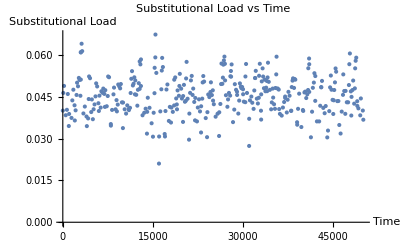

```mathematica
(* Plot Results of Simulation *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-0x10pn4_exp001.m"];
meansubload1=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
Print["mean substitutional load = ",meansubload1];
Print["mean q = ",meansubload1/Δc1];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time"]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension for second trait *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.00,0.02,0 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc2,U2,2];
```

Trait 1 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-0x10pn4_U2-1x10pn4_exp002.m",results];
```

mean substitutional load = 0.0799808

mean q = 3.99904

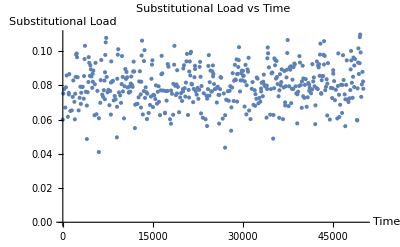

```mathematica
(* Plot Results of Simulation *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-0x10pn4_U2-1x10pn4_exp002.m"];
meansubload2=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
Print["mean substitutional load = ",meansubload2];
Print["mean q = ",meansubload2/Δc2];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time"]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution in 2 dimensions and store only summary data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,20000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.m",results];
```

mean substitution load = 0.07754

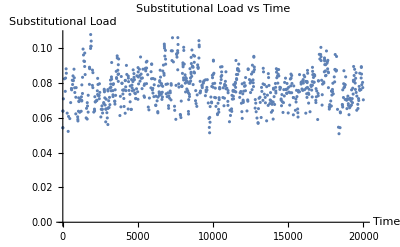

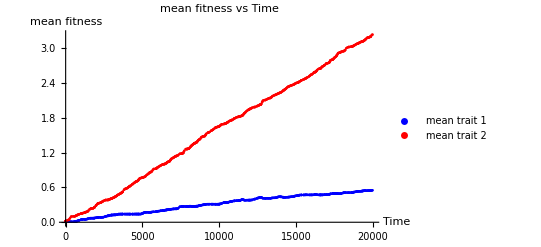

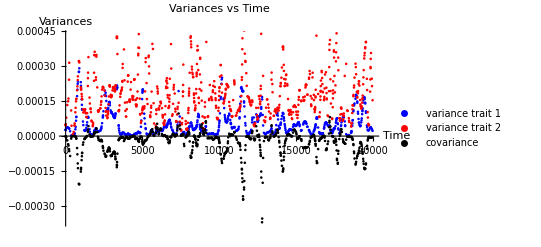

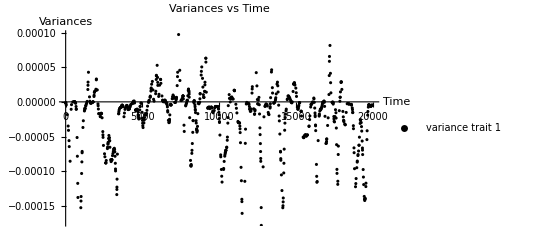

mean covariance -0.0000258785

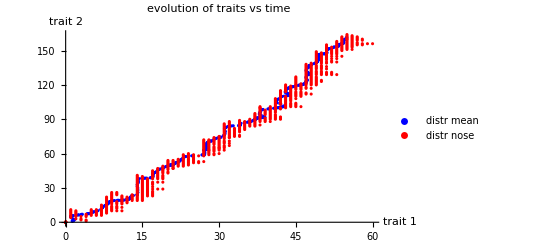

```mathematica
(* Plot Results of Simulation *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.m"];
meansubload=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
timesAndMean1=Table[{results[[i]][[1]],results[[i]][[2]]},{i,1,Length[results]}];
timesAndMean2=Table[{results[[i]][[1]],results[[i]][[3]]},{i,1,Length[results]}];
timesAndVar1=Table[{results[[i]][[1]],results[[i]][[6]]},{i,1,Length[results]}];
timesAndVar2=Table[{results[[i]][[1]],results[[i]][[7]]},{i,1,Length[results]}];
timesAndCov=Table[{results[[i]][[1]],results[[i]][[5]]},{i,1,Length[results]}];
mean2mean=Table[{results[[i]][[2]]/Δc1,results[[i]][[3]]/Δc2},{i,1,Length[results]}];
noseTravel=Table[results[[i]][[12]],{i,1,Length[results]}];
Print["mean substitution load = ",meansubload];
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time"]
ListPlot[{timesAndMean1,timesAndMean2},PlotStyle->{Blue,Red},PlotLegends->{"mean trait 1","mean trait 2"},AxesLabel->{"Time","mean fitness"},PlotLabel->"mean fitness vs Time"]
ListPlot[{timesAndVar1,timesAndVar2,timesAndCov},PlotStyle->{Blue,Red,Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"Variances vs Time"]
ListPlot[{timesAndCov},PlotStyle->{Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"Variances vs Time"]
Print["mean covariance ",Mean[timesAndCov[[;;,2]]]];
ListPlot[{mean2mean,noseTravel},PlotStyle->{Blue,Red},PlotLegends->{"distr mean","distr nose"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"evolution of traits vs time"]
```

```mathematica
(* Generate animation of details evolution of blob *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.m"];
mean2mean=Table[{results[[i]][[2]]/Δc1,results[[i]][[3]]/Δc2},{i,1,Length[results]}];
noseTravel=Table[results[[i]][[12]],{i,1,Length[results]}];
plots=Table[ListPlot[{mean2mean[[1;;i]],noseTravel[[1;;i]]},PlotStyle->{Black,Red},PlotRange->{{0,60},{0,150}},PlotLegends->{"distr mean","distr nose"},AxesLabel->{"trait 1","trait 2"},PlotLabel->{"evolution of traits vs time"}],{i,1,Length[mean2mean]}];
Export["~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.avi",plots]
```

~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.avi

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution in 2 dimensions and store full data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,20000}; 
{fulldata,verbose,veryverbose}={1,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.m",results];
```

```mathematica
(* Analyze Motion of blob *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.m"];
blob=results[[;;,{2,4,5}]];
Do[Do[
blob[[i]][[1]][[j]]=blob[[i]][[1]][[j]]-blob[[i]][[2]];
,{j,1,Length[blob[[i]][[1]]]}];
blob[[i]][[3]]=If[blob[[i]][[3]]=={0,0},{0,0},blob[[i]][[3]]-blob[[i]][[2]]];
,{i,1,Length[blob]}]
plots=Table[ListPlot[{blob[[i]][[1]],{blob[[i]][[3]]}},PlotStyle->{Black,Red},PlotRange->{{-5,7},{-5,7}},PlotMarkers->{Automatic,Large},PlotLegends->{"Fitness Classes","Mutant Fitness Class"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"Evolution of blob"],{i,1,Length[blob]}];
Export["~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.avi",plots];
```

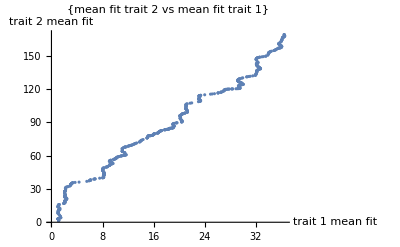

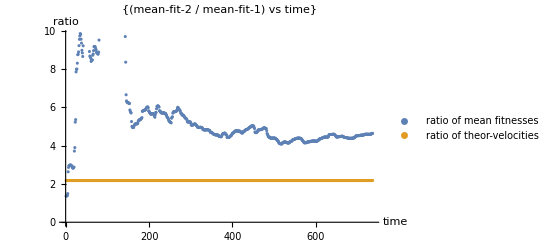

Total Fitness Increase = 3.74915 and predicted increase by theoretical sum of rate of increases is 6.03074

Trait 1 Fitness Increase = 0.364409 and predicted increase by theoretical rate of increase is 1.89607

Trait 2 Fitness Increase = 3.38475 and predicted increase by theoretical rate of increase is 4.13467

```mathematica
(* Examine Trajectories of Trait Mean Fitnesses *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,20000}; 
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.m"];
mean2mean=Table[({results[[i]][[3]]}.results[[i]][[2]])[[1]]/popsize,{i,1,Length[results]}];
meanratio=Table[mean2mean[[i]][[2]]/mean2mean[[i]][[1]],{i,1,Length[mean2mean]}];
velocityratio=Table[(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2)/(Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2),{i,1,Length[mean2mean]}];
ListPlot[mean2mean,PlotLabel->{"mean fit trait 2 vs mean fit trait 1"},AxesLabel->{"trait 1 mean fit","trait 2 mean fit"}]
ListPlot[{meanratio,velocityratio},PlotLegends->{"ratio of mean fitnesses","ratio of theor-velocities"},PlotLabel->{"(mean-fit-2 / mean-fit-1) vs time"},AxesLabel->{"time","ratio"}]
Print["Total Fitness Increase = ",mean2mean[[-1]][[1]]Δc1 +mean2mean[[-1]][[2]]Δc2 , " and predicted increase by theoretical sum of rate of increases is ",(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2+Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2)maxtime ]
Print["Trait 1 Fitness Increase = ",mean2mean[[-1]][[1]]Δc1 , " and predicted increase by theoretical rate of increase is ",(Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2)maxtime ]
Print["Trait 2 Fitness Increase = ",mean2mean[[-1]][[2]]Δc2 , " and predicted increase by theoretical rate of increase is ",(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2)maxtime ]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution in 2 dimensions and store full data with equal trait parameters *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactflag}={1,False,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactflag];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 4. in Concurrent Mutations Regime with expected time scale 153.506 and rate of adaptation 0.0000651442

Trait 2 q = 4. in Concurrent Mutations Regime with expected time scale 153.506 and rate of adaptation 0.0000651442

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp005.m",results];
```

```mathematica
(* Analyze Motion of blob *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp005.m"];
blob=results[[;;,{2,4,5}]];
Do[Do[
blob[[i]][[1]][[j]]=blob[[i]][[1]][[j]]-blob[[i]][[2]];
,{j,1,Length[blob[[i]][[1]]]}];
blob[[i]][[3]]=If[blob[[i]][[3]]=={0,0},{0,0},blob[[i]][[3]]-blob[[i]][[2]]];
,{i,1,Length[blob]}]
plots=Table[ListPlot[{blob[[i]][[1]],{blob[[i]][[3]]}},PlotStyle->{Black,Red},PlotRange->{{-5,7},{-5,7}},PlotMarkers->{Automatic,Large},PlotLegends->{"Fitness Classes","Mutant Fitness Class"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"Evolution of blob"],{i,1,Length[blob]}];
Export["~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp005.avi",plots];
Clear[plots];
```

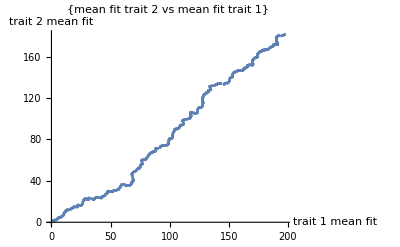

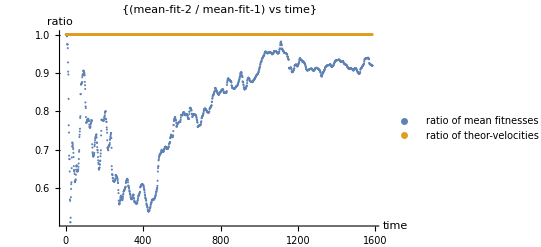

Total Fitness Increase = 3.78518 and predicted increase by theoretical sum of rate of increases is 6.51442

Trait 1 Fitness Increase = 1.97242 and predicted increase by theoretical rates of increase is 3.25721

Trait 2 Fitness Increase = 1.81276 and predicted increase by theoretical rate of increase is 3.25721

```mathematica
(* Examine Trajectories of Trait Mean Fitnesses *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp005.m"];
mean2mean=Table[({results[[i]][[3]]}.results[[i]][[2]])[[1]]/popsize,{i,1,Length[results]}];
meanratio=Table[mean2mean[[i]][[2]]/mean2mean[[i]][[1]],{i,1,Length[mean2mean]}];
velocityratio=Table[(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2)/(Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2),{i,1,Length[mean2mean]}];
ListPlot[mean2mean,PlotLabel->{"mean fit trait 2 vs mean fit trait 1"},AxesLabel->{"trait 1 mean fit","trait 2 mean fit"}]
ListPlot[{meanratio,velocityratio},PlotLegends->{"ratio of mean fitnesses","ratio of theor-velocities"},PlotLabel->{"(mean-fit-2 / mean-fit-1) vs time"},AxesLabel->{"time","ratio"}]
Print["Total Fitness Increase = ",mean2mean[[-1]][[1]]Δc1 +mean2mean[[-1]][[2]]Δc2 , " and predicted increase by theoretical sum of rate of increases is ",(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2+Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2)maxtime ]
Print["Trait 1 Fitness Increase = ",mean2mean[[-1]][[1]]Δc1 , " and predicted increase by theoretical rates of increase is ",(Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2)maxtime ]
Print["Trait 2 Fitness Increase = ",mean2mean[[-1]][[2]]Δc2 , " and predicted increase by theoretical rate of increase is ",(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2)maxtime ]
```

```mathematica
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,60000};
{fulldata,verbose,veryverbose}={0,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Testing two trait evolution *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Run Simulations *)
ParallelDo[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/convtest/convtest_N-10p6_c1-0d01_c2-0d02_U1-1x10pn4_U2-2x10pn4_exp"<>ToString[i]<>".dat",results,"Data"];
Print["exp ",i];
,{i,2,35}];
```

0.647534

7.40436

0.087453

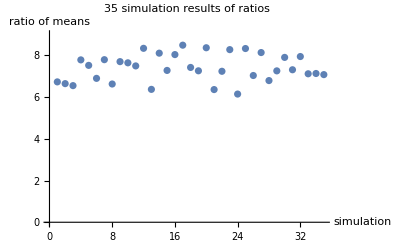

```mathematica
(* Analyzez convergence data *)
meanratios=Table[0,{i,1,35}];
Do[
results=Import["~/Documents/kgrel2d/data/convtest/convtest_N-10p6_c1-0d01_c2-0d02_U1-1x10pn4_U2-2x10pn4_exp"<>ToString[i]<>".dat"];
meanratios[[i]]=results[[-1]][[3]]/results[[-1]][[2]];
,{i,1,35}];
StandardDeviation[meanratios]
Mean[meanratios]
StandardDeviation[meanratios]/Mean[meanratios]
ListPlot[meanratios,PlotRange->{0,9},PlotLabel->"35 simulation results of ratios",AxesLabel-> {"simulation","ratio of means"}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution in 2 dimensions and store full data with one dimension in successional regime *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-8,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose}={1,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,False];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{1,4},{1,5},{1,6}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 1.33333 in Successional Regime with expected time scale 4144.65 and rate of adaptation 2.41275×10^-6

Trait 2 q = 4. in Concurrent Mutations Regime with expected time scale 153.506 and rate of adaptation 0.0000651442

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn8_U2-1x10pn4_exp013.m",results];
```

```mathematica
(* Analyze Motion of blob *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn8_U2-1x10pn4_exp013.m"];
blob=results[[;;,{2,4,5}]];
Do[Do[
blob[[i]][[1]][[j]]=blob[[i]][[1]][[j]]-blob[[i]][[2]];
,{j,1,Length[blob[[i]][[1]]]}];
blob[[i]][[3]]=If[blob[[i]][[3]]=={0,0},{0,0},blob[[i]][[3]]-blob[[i]][[2]]];
,{i,1,Length[blob]}]
plots=Table[ListPlot[{blob[[i]][[1]],{blob[[i]][[3]]}},PlotStyle->{Black,Red},PlotRange->{{-5,7},{-5,7}},PlotMarkers->{Automatic,Large},PlotLegends->{"Fitness Classes","Mutant Fitness Class"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"Evolution of blob"],{i,1,Length[blob]}];
Export["~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn8_U2-1x10pn4_exp013.avi",plots];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6a *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,21}];
simq=Table[{},{i,1,21}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

```mathematica
(* Run simulation *)
Do[
results=RunSimulationCheckEachMutation2[10^(4+((j-1)/5)),Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,10^(4+((j-1)/5))/popsize genotypeabundances][[2]][[1]];
simv[[j]]={(4+((j-1)/5)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]};
simq[[j]]={(4+((j-1)/5)),Mean[results[[;;,9]]]/Δc1};
,{j,1,21}];
thryvest=Table[{(4+(j/25)),(10^5 Δc1^2(2 Log[Δc1 10^(4+(j/25))]-Log[Δc1/U1]))/Log[Δc1/U1]^2},{j,0,100}];
thryvext=Table[{(4+(j/25)),10^5 getTransV[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
thryqest=Table[{(4+(j/25)),2((4+((j-1)/25))-2)/3},{j,0,100}];
thryqext=Table[{(4+(j/25)),getTransQ[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp006.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

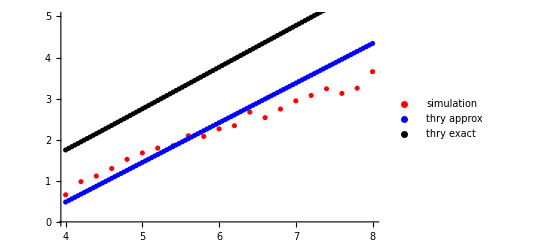

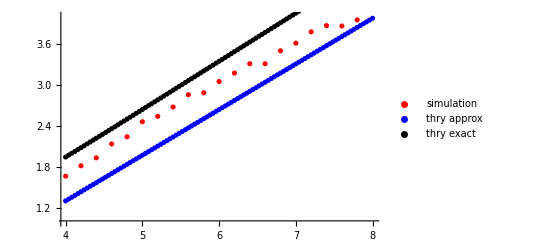

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp006.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,5}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,4}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 b *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-4,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,21}];
simq=Table[{},{i,1,21}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

```mathematica
(* Run simulation *)
Do[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,10^(-4-((j-1)/10)),U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
simv[[j]]={(-4-((j-1)/10)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]};
simq[[j]]={(-4-((j-1)/10)),Mean[results[[;;,9]]]/Δc1};
,{j,1,21}];
thryvest=Table[{(-4-(i/50)),(10^5 Δc1^2(2 Log[popsize Δc1]-Log[Δc1/10^(-4-(i/50))]))/(Log[Δc1/10^(-4-(i/50))]^2)},{i,0,100}];
thryvext=Table[{(-4-(i/50)),10^5 getTransV[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
thryqest=Table[{(-4-(i/50)),-8/((-4-(i/50))+2)},{i,0,100}];
thryqext=Table[{(-4-(i/50)),getTransQ[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp007.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

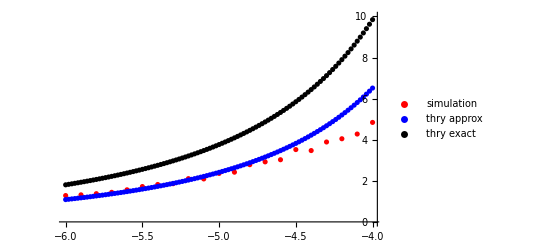

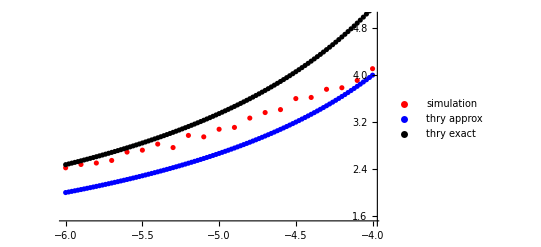

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp007.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,10}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1.5,5}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 c *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,21}];
simq=Table[{},{i,1,21}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

```mathematica
(* Run simulation *)
Do[
results=RunSimulationCheckEachMutation2[popsize,10^(-13/4+(j-1)/10),Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
simv[[j]]={(-13/4+(j-1)/10),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]};
simq[[j]]={(-13/4+(j-1)/10),Mean[results[[;;,9]]]/10^(-13/4+(j-1)/10)};
,{j,1,21}];
thryvest=Table[{(-13/4+(i/50)),(10^5 10^(2(-13/4+i/50))(2 Log[popsize 10^(-13/4+i/50)]-Log[10^(-13/4+i/50)/U1]))/(Log[10^(-13/4+i/50)/U1]^2)},{i,0,100}];
thryvext=Table[{(-13/4+(i/50)),10^5 getTransV[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
thryqest=Table[{(-13/4+(i/50)),(2 Log[popsize 10^(-13/4+i/50)])/Log[10^(-13/4+i/50)/U1]},{i,0,100}];
thryqext=Table[{(-13/4+(i/50)),getTransQ[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp008.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

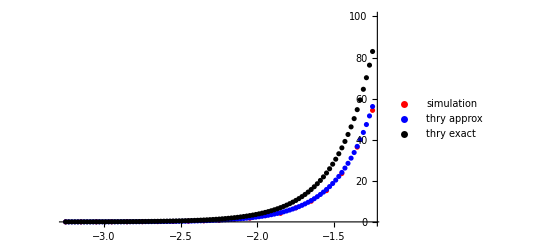

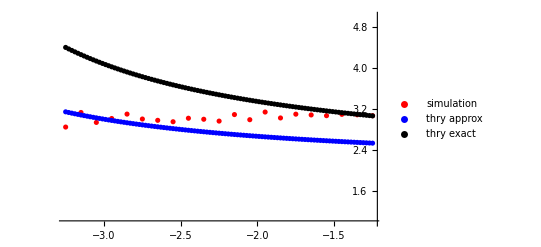

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp008.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,100}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,5}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 c *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.001,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={1,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={1,False,False,False};
(* Set initial genotypes and their abundances *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,False];
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

Trait 1 q = 3. in Concurrent Mutations Regime with expected time scale 2302.59 and rate of adaptation 4.34294×10^-7

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

```mathematica
(* Run simulation *)
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d001_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp009.m",results];
```

```mathematica
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d001_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp009.m"];
qresults=getSummarizedResults[results,Δc1,Δc2,popsize][[;;,{1,9,11}]];
qresults[[;;,2]]=Δc1^-1 qresults[[;;,2]];
```

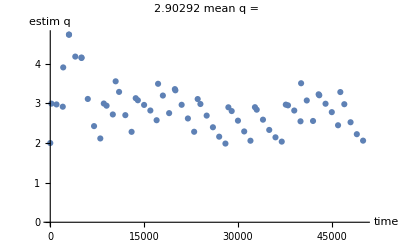

genotypes = {{1,1},{2,1},{3,1},{4,1}}

mutant genotypes {{1,1},{2,1},{3,1},{4,1},{5,1},{1,2},{2,2},{3,2},{4,2}}

abundances = {0.980391,9803.91,980391.,9803.91}

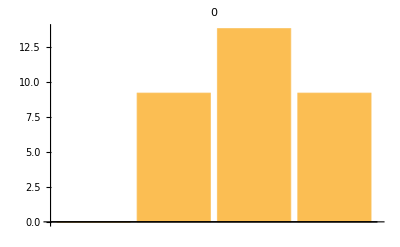

```mathematica
timeIndx=1;
ListPlot[qresults[[;;,{1,2}]],AxesLabel->{"time","estim q"},PlotLabel->"mean q = "ToString[Mean[qresults[[;;,2]]]]]
Print["genotypes = ",results[[timeIndx]][[2]]];
Print["mutant genotypes ",qresults[[timeIndx]][[3]]];
Print["abundances = ",results[[timeIndx]][[3]]];
BarChart[Log[N[results[[timeIndx]][[3]],16]],PlotLabel->ToString[results[[timeIndx]][[1]]]]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 a Examine Statistical Spread*)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,210}];
simq=Table[{},{i,1,210}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
```

```mathematica
(* Run simulation *)
simdata =ParallelTable[
results=RunSimulationCheckEachMutation2[10^(4+((Mod[j,21,1]-1)/5)),Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,10^(4+((Mod[j,21,1]-1)/5))/popsize genotypeabundances][[2]][[1]];
{{(4+((Mod[j,21,1]-1)/5)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]},{(4+((Mod[j,21,1]-1)/5)),Mean[results[[;;,9]]]/Δc1}}
,{j,1,210}];
simv=simdata[[;;,1]];
simq=simdata[[;;,2]];
```

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp010.m"];
thryvest=Table[{(4+(j/25)),(10^5 Δc1^2(2 Log[Δc1 10^(4+(j/25))]-Log[Δc1/U1]))/Log[Δc1/U1]^2},{j,0,100}];
thryvext=Table[{(4+(j/25)),10^5 getTransV[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
thryqest=Table[{(4+(j/25)),2((4+((j-1)/25))-2)/3},{j,0,100}];
thryqext=Table[{(4+(j/25)),getTransQ[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp010.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

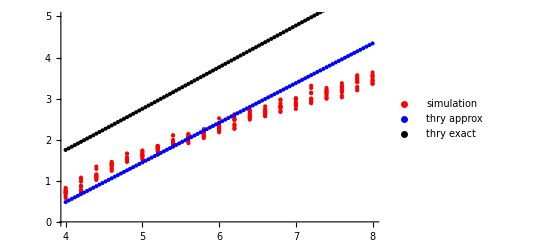

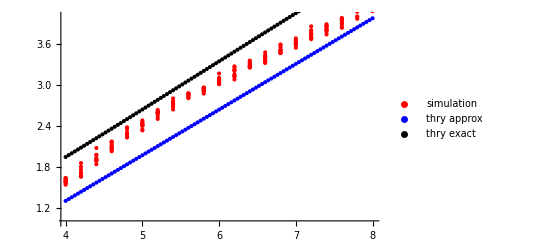

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp010.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,5}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,4}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 b *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-4,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,210}];
simq=Table[{},{i,1,210}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
```

```mathematica
(* Run simulation *)
simdata=ParallelTable[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,10^(-4-((Mod[j,21,1]-1)/10)),U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
{{(-4-((Mod[j,21,1]-1)/10)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]},{(-4-((Mod[j,21,1]-1)/10)),Mean[results[[;;,9]]]/Δc1}}
,{j,1,210}];
simv=simdata[[;;,1]];
simq=simdata[[;;,2]];
```

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp011.m"];
thryvest=Table[{(-4-(i/50)),(10^5 Δc1^2(2 Log[popsize Δc1]-Log[Δc1/10^(-4-(i/50))]))/(Log[Δc1/10^(-4-(i/50))]^2)},{i,0,100}];
thryvext=Table[{(-4-(i/50)),10^5 getTransV[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
thryqest=Table[{(-4-(i/50)),-8/((-4-(i/50))+2)},{i,0,100}];
thryqext=Table[{(-4-(i/50)),getTransQ[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp011.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

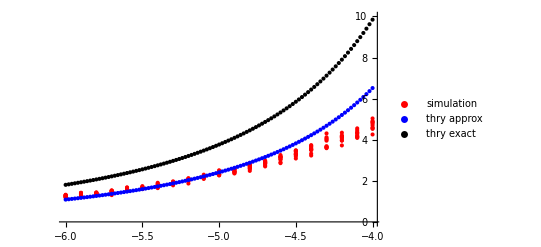

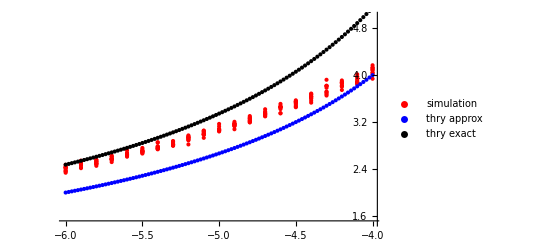

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp011.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,10}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1.5,5}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 c *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,210}];
simq=Table[{},{i,1,210}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
```

```mathematica
(* Run simulation *)
simdata=ParallelTable[
results=RunSimulationCheckEachMutation2[popsize,10^(-13/4+(Mod[j,21,1]-1)/10),Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
{{(-13/4+(Mod[j,21,1]-1)/10),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]},{(-13/4+(Mod[j,21,1]-1)/10),Mean[results[[;;,9]]]/10^(-13/4+(Mod[j,21,1]-1)/10)}}
,{j,1,210}];
simv=simdata[[;;,1]];
simq=simdata[[;;,2]];
```

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp012.m"];
thryvest=Table[{(-13/4+(i/50)),(10^5 10^(2(-13/4+i/50))(2 Log[popsize 10^(-13/4+i/50)]-Log[10^(-13/4+i/50)/U1]))/(Log[10^(-13/4+i/50)/U1]^2)},{i,0,100}];
thryvext=Table[{(-13/4+(i/50)),10^5 getTransV[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
thryqest=Table[{(-13/4+(i/50)),(2 Log[popsize 10^(-13/4+i/50)])/Log[10^(-13/4+i/50)/U1]},{i,0,100}];
thryqext=Table[{(-13/4+(i/50)),getTransQ[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp012.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

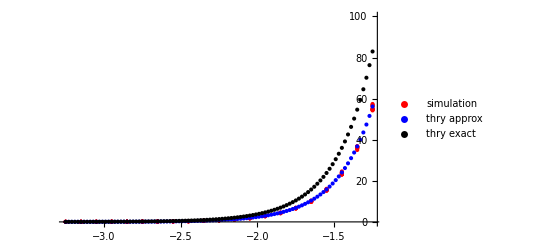

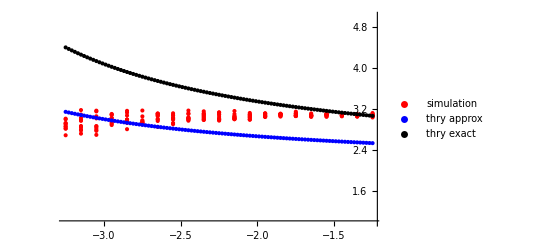

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp012.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,100}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,5}]
```

```mathematica
(* Testing Time Until Establishment from Simulation with Results from Desai and Fisher *)
(* Checking deviations in High N range 10^8, I am going to measure the time between the first establishment and the second *)
(* Also, comparing with data that does fall in the right range *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^8};
{starttime,timestep,maxtime}={0,1000,200000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,True};
(* Get theoretical estimates for q and v *)
Print["Approximate estimates for q and v "]
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,False];
Print["Exact estimates for q and v "]
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
```

Approximate estimates for q and v

Trait 1 q = 4. in Concurrent Mutations Regime with expected time scale 230.259 and rate of adaptation 0.0000434294

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

Exact estimates for q and v

Trait 1 q = 4.74803 in Concurrent Mutations Regime with expected time scale 184.303 and rate of adaptation 0.0000542583

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

```mathematica
simdata=ParallelTable[
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
results
,{i,1,4}];
Export["~/Documents/kgrel2d/data/tautest/tautest_N-10p8_c-0d01_U-1x10pn5_exp001.m",simdata];
```

Approximate estimates for τ

Expected τ = 212.359, with variance = 799.621

Exact estimates for τ

Expected τ = 172.774, with variance = 441.298

Simulation estimates for τ

Mean τ = 283.455, with variance = 7271.18, from 2818 samples points.

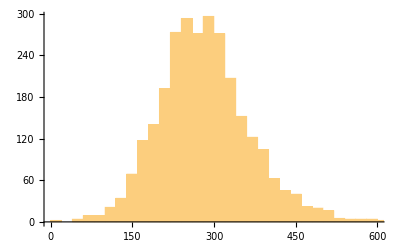

```mathematica
simdata=Import["~/Documents/kgrel2d/data/tautest/tautest_N-10p8_c-0d01_U-1x10pn5_exp001.m"];
tauqs={};
Do[
simdata[[i]]=Select[simdata[[i]],(#[[12]]≠ {0,0})&];
tauqs=Join[tauqs,Table[simdata[[i]][[j]][[1]]-simdata[[i]][[j-1]][[1]],{j,2,Length[simdata[[i]]]}]];
,{i,1,4}]
Print["Approximate estimates for τ "]
PrintTauDetails[Δc1,U1,popsize,False];
Print["Exact estimates for τ "]
PrintTauDetails[Δc1,U1,popsize,exactqv];
Print["Simulation estimates for τ "]
Print["Mean τ = ",Mean[tauqs],", with variance = ",Variance[tauqs],", from ",Length[tauqs]," samples points."];
Histogram[tauqs]
```

```mathematica
qss=getTransQ[Δc1,U1,popsize,False];
pFix=qss Δc1/(1+qss Δc1);
f1[t_]:=U1/(pFix)Exp[(qss-1)Δc1 t]; 
pdf1[t_]:=pFix f1[t] Exp[-pFix Integrate[f1[w],{w,0,t}]];
tmean=NIntegrate[t pdf1[t],{t,0,Infinity}]
tvar=NIntegrate[(t-tmean)^2 pdf1[t],{t,0,20000}]
```

247.732

1801.61

```mathematica
(* Checking deviations in good N range 10^6, I am going to measure the time between the first establishment and the second *)
(* Also, comparing with data that does fall in the right range *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,400000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,True};
(* Get theoretical estimates for q and v *)
Print["Approximate estimates for q and v "]
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,False];
Print["Exact estimates for q and v "]
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
```

Approximate estimates for q and v

Trait 1 q = 2.66667 in Concurrent Mutations Regime with expected time scale 414.465 and rate of adaptation 0.0000241275

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

Exact estimates for q and v

Trait 1 q = 3.34524 in Concurrent Mutations Regime with expected time scale 294.544 and rate of adaptation 0.0000339508

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

```mathematica
simdata=ParallelTable[
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
results
,{i,1,4}];
Export["~/Documents/kgrel2d/data/tautest/tautest_N-10p6_c-0d01_U-1x10pn5_exp002.m",simdata];
```

Approximate estimates for τ

Expected τ = 358.693, with variance = 3608.57

Exact estimates for τ

Expected τ = 265.58, with variance = 1520.79

Simulation estimates for τ

Mean τ = 437.347, with variance = 23490., from 3653 samples points.

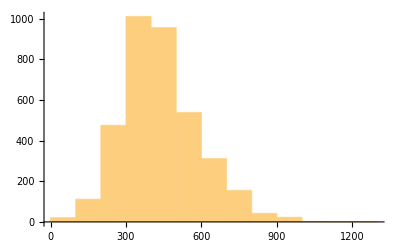

```mathematica
simdata=Import["~/Documents/kgrel2d/data/tautest/tautest_N-10p6_c-0d01_U-1x10pn5_exp002.m"];
tauqs={};
Do[
simdata[[i]]=Select[simdata[[i]],(#[[12]]≠ {0,0})&];
tauqs=Join[tauqs,Table[simdata[[i]][[j]][[1]]-simdata[[i]][[j-1]][[1]],{j,2,Length[simdata[[i]]]}]];
,{i,1,4}]
Print["Approximate estimates for τ "]
PrintTauDetails[Δc1,U1,popsize,False];
Print["Exact estimates for τ "]
PrintTauDetails[Δc1,U1,popsize,exactqv];
Print["Simulation estimates for τ "]
Print["Mean τ = ",Mean[tauqs],", with variance = ",Variance[tauqs],", from ",Length[tauqs]," samples points."];
Histogram[tauqs]
```

```mathematica
(* Some theoretical estimates *)
qss=getTransQ[Δc1,U1,popsize,False];
pFix=qss Δc1/(1+qss Δc1);
f1[t_]:=U1/(pFix)Exp[(qss-1)Δc1 t]; 
pdf1[t_]:=pFix f1[t] Exp[-pFix Integrate[f1[w],{w,0,t}]];
tmean=NIntegrate[t pdf1[t],{t,0,Infinity}]
tvar=NIntegrate[(t-tmean)^2 pdf1[t],{t,0,20000}]
```

410.764

5790.22

```mathematica
(* Testing Time Until Establishment from Simulation with Results from Desai and Fisher checking fitness variance *)
(* Checking deviations in High N range 10^8, I am going to measure the time between the first establishment and the second *)
(* Also, comparing with data that does fall in the right range *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^8};
{starttime,timestep,maxtime}={0,1000,200000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,True};
(* Get theoretical estimates for q and v *)
Print["Approximate estimates for q and v "]
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,False];
Print["Exact estimates for q and v "]
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
```

Approximate estimates for q and v

Trait 1 q = 4. in Concurrent Mutations Regime with expected time scale 230.259 and rate of adaptation 0.0000434294

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

Exact estimates for q and v

Trait 1 q = 4.74803 in Concurrent Mutations Regime with expected time scale 184.303 and rate of adaptation 0.0000542583

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

```mathematica
simdata=ParallelTable[
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
results
,{i,1,4}];
Export["~/Documents/kgrel2d/data/tautest/tautest_N-10p8_c-0d01_U-1x10pn5_exp003.m",simdata];
```

```mathematica
simdata=Import["~/Documents/kgrel2d/data/tautest/tautest_N-10p8_c-0d01_U-1x10pn5_exp001.m"];
varvs={};
tauvs={};
endvs={};
Do[
endvs=Join[endvs,{(simdata[[i]][[-1]][[4]]-simdata[[i]][[1]][[4]])/simdata[[i]][[-1]][[1]]}];
varvs=Join[varvs,{Table[10^5 simdata[[i]][[j]][[6]],{j,1,Length[simdata[[i]]]}]}];
simdata[[i]]=Select[simdata[[i]],(#[[12]]≠ {0,0})&];
tauvs=Join[tauvs,{simdata[[i]][[2;;-1,1]]-simdata[[i]][[1;;-2,1]]}];
,{i,1,4}]
Print["Simulation estimates for using endpoints v ",10^5 endvs[[1]]]
Print["Simulation estimates for using taus v ",10^5 Δc1/Mean[tauvs[[1]]]]
Print["Simulation estimates for using variance v ",Mean[varvs[[1]]]]
```

Simulation estimates for using endpoints v 3.47571

Simulation estimates for using taus v 3.47524

Simulation estimates for using variance v 3.53585

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution in 2 dimensions size of front *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Analyze Motion of blob *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.m"];

blob=results[[;;,{2,4,5}]];
Do[Do[
blob[[i]][[1]][[j]]=blob[[i]][[1]][[j]]-blob[[i]][[2]];
,{j,1,Length[blob[[i]][[1]]]}];
blob[[i]][[3]]=If[blob[[i]][[3]]=={0,0},{0,0},blob[[i]][[3]]-blob[[i]][[2]]];
,{i,1,Length[blob]}]
plots=Table[ListPlot[{blob[[i]][[1]],{blob[[i]][[3]]}},PlotStyle->{Black,Red},PlotRange->{{-5,7},{-5,7}},PlotMarkers->{Automatic,Large},PlotLegends->{"Fitness Classes","Mutant Fitness Class"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"Evolution of blob"],{i,1,Length[blob]}];
Export["~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.avi",plots];
```

```mathematica
(* Examine Trajectories of Trait Mean Fitnesses *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,20000}; 
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.m"];
mean2mean=Table[({results[[i]][[3]]}.results[[i]][[2]])[[1]]/popsize,{i,1,Length[results]}];
meanratio=Table[mean2mean[[i]][[2]]/mean2mean[[i]][[1]],{i,1,Length[mean2mean]}];
velocityratio=Table[(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2)/(Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2),{i,1,Length[mean2mean]}];
ListPlot[mean2mean,PlotLabel->{"mean fit trait 2 vs mean fit trait 1"},AxesLabel->{"trait 1 mean fit","trait 2 mean fit"}]
ListPlot[{meanratio,velocityratio},PlotLegends->{"ratio of mean fitnesses","ratio of theor-velocities"},PlotLabel->{"(mean-fit-2 / mean-fit-1) vs time"},AxesLabel->{"time","ratio"}]
Print["Total Fitness Increase = ",mean2mean[[-1]][[1]]Δc1 +mean2mean[[-1]][[2]]Δc2 , " and predicted increase by theoretical sum of rate of increases is ",(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2+Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2)maxtime ]
Print["Trait 1 Fitness Increase = ",mean2mean[[-1]][[1]]Δc1 , " and predicted increase by theoretical rate of increase is ",(Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2)maxtime ]
Print["Trait 2 Fitness Increase = ",mean2mean[[-1]][[2]]Δc2 , " and predicted increase by theoretical rate of increase is ",(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2)maxtime ]
```

-Graphics-

-Graphics-

Total Fitness Increase = 3.74915 and predicted increase by theoretical sum of rate of increases is 6.03074

Trait 1 Fitness Increase = 0.364409 and predicted increase by theoretical rate of increase is 1.89607

Trait 2 Fitness Increase = 3.38475 and predicted increase by theoretical rate of increase is 4.13467

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Later use this to check against Ben's code v's and theoretical*)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,0.00001,0,1000000000};
{starttime,timestep,maxtime}={0,1000,80000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,False]
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,True]
```

Trait 1 q = 4.66667 in Concurrent Mutations Regime with expected time scale 188.393 and rate of adaptation 0.0000530804

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

Trait 1 q = 5.44507 in Concurrent Mutations Regime with expected time scale 155.402 and rate of adaptation 0.000064349

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

```mathematica
sim=ParallelTable[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]
,{j,1,5}];
Print["Simulated v's = ",sim, " with mean v = ",Mean[sim]];
```

Simulated v's = {4.07601,4.1476,4.03936,4.11024,4.03174} with mean v = 4.08099

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
SolveDiffEqsFreq[popsize_,Δc1_,Δc2_,genotypeabundances_,genotypes_,timestep_]:=Module[
(* LOCAL VARIABLES*)
{C,diffeqarray,X,system,sol,numgenotypes,rbar},

(* INITIALIZE LOCAL VARIABLES *)
C=genotypeabundances[[1]];
numgenotypes=getNumGenotypes[genotypes];

(* SOLVE DETERMINISTIC EQUATIONS *)
If[numgenotypes==1
,(* IF ONLY ONE GENOTYPE, THEN USE EXACT SOLUTION *)
system={n1'[t]==n1[t](1+genotypes[[1]][[1]]Δc1+genotypes[[1]][[2]]Δc2)(1-n1[t]/popsize),n1[0]==C};
sol={{n1[t]->popsize/((popsize/C-1)Exp[-(1+genotypes[[1]][[1]]Δc1+genotypes[[1]][[2]]Δc2)t]+1)}};
,(* ELSE MORE THAN ONE GENOTYPE SO FORM DERIVATIVE AND HAVE MATHEMATICA SOLVE THE SYSTEM *)
X[t_]=ToExpression["n"<>ToString[#]<>"[t]"]&/@Range[numgenotypes];
rbar[t_]=Sum[(1+genotypes[[i]][[1]]Δc1+genotypes[[i]][[2]]Δc2)X[t][[i]],{i,numgenotypes}]/Total[X[t]];
diffeqarray=Table[X[t][[i]](1+genotypes[[i]][[1]]Δc1+genotypes[[i]][[2]]Δc2-rbar[t]),{i,numgenotypes}];
system = Join[
MapThread[#1==#2&,{D[X[t],t],diffeqarray}],(*see tutorial/DSolveSystemsOfLinearODEs*)
MapThread[#1==#2&,{X[t]/.t->0,genotypeabundances}]];
sol=NDSolve[system, X[t],{t,0,timestep}];];

(* RETURN: SYSTEM AND SOLUTION *)
{system,sol}
]
(* Testing SystemSolver, SolveDiffEqs *)
{Δc1,Δc2,U1,U2,popsize,timestep}={0.01,0.00,0.00001,0,1000000000,1500}; 
(* Testing system solver for one fitness class *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1]
{system,sol}=SolveDiffEqsFreq[popsize,Δc1,Δc2,(1/popsize)*genotypeabundances,genotypes,timestep];
detResults=Table[Join[{50i},Table[popsize*((ToExpression["n"<>ToString[j]<>"[t]"]/.sol[[1]])/.t->50i),{j,1,Length[genotypes]}]],{i,0,30}];
```

{{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1}},{0.0831945,831.945,831945.,8.31945×10^7,8.31945×10^8,8.31945×10^7,831945.,831.945}}

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Later use this to check against Ben's code v's and theoretical*)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,0.00001,0,1000000000};
{starttime,timestep,maxtime}={0,50,1500}; 
{fulldata,verbose,veryverbose,exactqv}={1,False,False,False};
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1]
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,0,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
results=Table[Join[{results[[i]][[1]]},Table[0,{j,1,Length[genotypes]-Length[results[[i]][[3]]]}],results[[i]][[3]]],{i,1,Length[results]}];
```

{{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1}},{0.0831945,831.945,831945.,8.31945×10^7,8.31945×10^8,8.31945×10^7,831945.,831.945}}

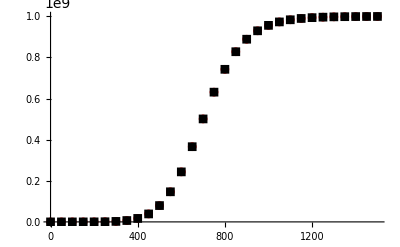

```mathematica
fc=9;
ListPlot[
{Table[{detResults[[i]][[1]],detResults[[i]][[fc]]},{i,1,Length[detResults]}],
Table[{results[[i]][[1]],results[[i]][[fc]]},{i,1,Length[results]}]},PlotStyle->{Red,Black},PlotMarkers->Automatic
]
```

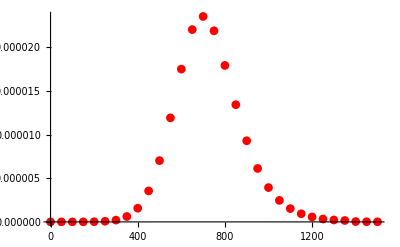

```mathematica
fc=9;
ListPlot[
{Table[{detResults[[i]][[1]],(detResults[[i]][[fc]]-results[[i]][[fc]])/popsize},{i,1,Length[results]}]},PlotStyle->{Red,Black},PlotMarkers->Automatic
]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Later use this to check against Ben's code v's and theoretical*)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={10.0^-2,0.0,10.0^-6,0.0,10.0^4};
{starttime,timestep,maxtime}={0,1000,25000000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}={{{1,1}},{popsize}};
SeedRandom[7];
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,False]
(*printRegimeDetails[Δc1,Δc2,U1,U2,popsize,True]*)
```

Trait 1 q = 1. in Successional Regime with expected time scale -8.29594×10^18 and rate of adaptation -1.20541×10^-21

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

```mathematica
sim=ParallelTable[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]
,{j,1,1}];
Print["Simulated v's = ",N[sim,32], " with mean v = ",Mean[sim]];
```

Simulated v's = {0.09536} with mean v = 0.09536

```mathematica
N[10^5 popsize U1 Δc1^2,16]
(Mean[sim]-N[10^5 popsize U1 Δc1^2,16])/Mean[sim]
```

0.1

-0.0486577

```mathematica
probt[t_]:=Δc1/Gamma[popsize U1] Exp[-popsize U1 Δc1 t-Exp[-Δc1 t]]
Integrate[t probt[t],{t,-Infinity,Infinity}]
```

10056.1

```mathematica
10^5(Δc1/10056.2)
```

0.0994411

```mathematica
Array[(0 #1 #2) &,{2,3}]
```

{{0,0,0},{0,0,0}}

```mathematica
(* Testing Code for linkage disequilibria matrix *)
{Δc1,Δc2,U1,U2,popsize}={10.0^-2,10.0^-2,10.0^-4,10.0^-4,10.0^6};
{starttime,timestep,maxtime}={0,1000,25000000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
```

```mathematica
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[5,popsize,Δc1,Δc2,U1,U2];
genotypes=Join[genotypes[[1;;3]],genotypes[[5;;-1]]]
genotypeabundances=Join[genotypeabundances[[1;;3]],genotypeabundances[[5;;-1]]]
```

{{1,1},{1,2},{1,3},{1,5},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{4,1},{4,2},{5,1}}

{665799.,143442.,6657.99,0.143442,143442.,30903.6,1434.42,14.3442,6657.99,1434.42,66.5799,66.5799,14.3442,0.143442}

```mathematica
{genotypes,genotypeabundances}=getInitial2Ddistribution[5,popsize,Δc1,Δc2,U1,U2];
genotypes=genotypes[[1;;-2]]
genotypeabundances=genotypeabundances[[1;;-2]]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{4,1},{4,2}}

{665799.,143442.,6657.99,66.5799,0.143442,143442.,30903.6,1434.42,14.3442,6657.99,1434.42,66.5799,66.5799,14.3442}

```mathematica
unitmatrix=Array[(1+0#1 #2) &,{Max[genotypes[[;;,1]]]-Min[genotypes[[;;,1]]]+1,Max[genotypes[[;;,2]]]-Min[genotypes[[;;,2]]]+1}]ᵀ;
genotypefrequencies=Array[(0#1 #2) &,{Max[genotypes[[;;,1]]]-Min[genotypes[[;;,1]]]+1,Max[genotypes[[;;,2]]]-Min[genotypes[[;;,2]]]+1}];
Do[genotypefrequencies[[genotypes[[k]][[1]],genotypes[[k]][[2]]]]=genotypeabundances[[k]],{k,1,Length[genotypes]}];
genotypefrequencies=(1/Total[Flatten[genotypefrequencies]])genotypefrequencies;
linkagedisequilibria=genotypefrequencies-(genotypefrequencies.unitmatrix).genotypefrequencies;
genotypefrequencies//MatrixForm
unitmatrix//MatrixForm
linkagedisequilibria//MatrixForm
```

(0.665799 | 0.143442 | 0.00665799 | 0.0000665799 | 1.43442×10^-7
0.143442 | 0.0309036 | 0.00143442 | 0.0000143442 | 0.
0.00665799 | 0.00143442 | 0.0000665799 | 0. | 0.
0.0000665799 | 0.0000143442 | 0. | 0. | 0.)

(1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1)

(-9.12549×10^-7 | -1.96603×10^-7 | 5.34144×10^-7 | 5.4861×10^-7 | 2.63983×10^-8
-1.71387×10^-7 | -3.69241×10^-8 | 1.1533×10^-7 | 1.18197×10^-7 | -2.52163×10^-8
5.35314×10^-7 | 1.1533×10^-7 | 1.07854×10^-8 | -6.60259×10^-7 | -1.17034×10^-9
5.48622×10^-7 | 1.18197×10^-7 | -6.60259×10^-7 | -6.54871×10^-9 | -1.16079×10^-11)

```mathematica
truepopsize=Total[genotypeabundances];
trait1meanfitness=Δc1 Sum[genotypes[[i]][[1]]genotypeabundances[[i]]/truepopsize,{i,1,Length[genotypes]}];
trait2meanfitness=Δc2 Sum[genotypes[[i]][[2]]genotypeabundances[[i]]/truepopsize,{i,1,Length[genotypes]}];
meanfitness=1+trait1meanfitness+trait2meanfitness;
traitfitnesscovariances=(Sum[(Δc1 genotypes[[i]][[1]]-trait1meanfitness)(Δc2 genotypes[[i]][[2]] -trait2meanfitness)genotypeabundances[[i]]/truepopsize,{i,1,Length[genotypes]}]) ;
trait1fitnessvariance=Sum[(Δc1 genotypes[[i]][[1]]-trait1meanfitness)^2 genotypeabundances[[i]]/truepopsize,{i,1,Length[genotypes]}];
trait2fitnessvariance=Sum[(Δc2 genotypes[[i]][[2]]-trait2meanfitness)^2 genotypeabundances[[i]]/truepopsize,{i,1,Length[genotypes]}];
fitnessvariance=Sum[(1+Δc1 genotypes[[i]][[1]]+Δc2 genotypes[[i]][[2]]-meanfitness)^2 genotypeabundances[[i]]/truepopsize,{i,1,Length[genotypes]}];
```

```mathematica
trait1meanfitness
trait2meanfitness
traitfitnesscovariances
r1=Table[{Δc1 i-trait1meanfitness},{i,Min[genotypes[[;;,1]]],Max[genotypes[[;;,1]]]}]
r2=Table[{Δc2 i-trait2meanfitness},{i,Min[genotypes[[;;,2]]],Max[genotypes[[;;,2]]]}]
r1ᵀ.linkagedisequilibria.r2
```

0.0119236

0.0119236

-6.91569×10^-10

{{-0.00192355},{0.00807645},{0.0180764},{0.0280764}}

{{-0.00192356},{0.00807644},{0.0180764},{0.0280764},{0.0380764}}

{{-6.91569×10^-10}}

```mathematica
(* Testing Selection's contribution to linkage disequilibria matrix *)
{Δc1,Δc2,U1,U2,popsize}={10.0^-2,5 10.0^-2,10.0^-4,10.0^-4,10.0^6};
{starttime,timestep,maxtime}={0,0.01,1}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
SeedRandom[7];
genotypes={};
Do[Do[genotypes=Join[genotypes,{{i,j}}];,{i,10,19}],{j,10,19}];
genotypeabundances=Table[1/100,{k,1,100}];
```

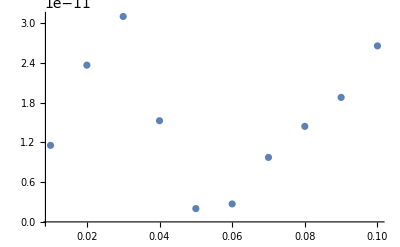

```mathematica
(* {genotypes,genotypeabundances}=getRandomFitDistr[popsize,{10,50},{10,20},0]; *)
(* {genotypes,genotypeabundances}=getInitial2Ddistribution[5,popsize,Δc1,Δc2,U1,U2]; *)
result=myCovDSelectionTest[popsize,Δc1,Δc2,genotypes,genotypeabundances,maxtime,timestep];
ListPlot[Table[{result[[i]][[1]],result[[i]][[2]]},{i,1,10}],PlotRange->All]
```

```mathematica
{Δc1,Δc2,U1,U2,popsize}={1.0 10^-3,1.0 10^-3,1.0 10^-7,1 10^-7,1.0 10^13};
Print["Branch Proc. works if: ",1," << ",popsize Δc1," << ",popsize];
Print["Strong mut. regime if: ",popsize 2U1," >> ",1];
Print["Clonal interference if: ",popsize 2U1 Log[popsize Δc1],">>",1];
Print[ "q larger than two if: ",Log[popsize Δc1],">=",Log[Δc1/(2U1)]];
Print["Large cross-diag if: ",Log[Δc1/(2U1)]^2, ">>",2Log[popsize Δc1]];
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,False];
printRegimeDetails[Δc1,0,2U1,0,popsize,False];
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,2U1,1];
(1/Total[genotypeabundances])genotypeabundances
genotypeabundances
```

Branch Proc. works if: 1 << 1.×10^10 << 1.×10^13

Strong mut. regime if: 2.×10^6 >> 1

Clonal interference if: 4.60517×10^7>>1

q larger than two if: 23.0259>=8.51719

Large cross-diag if: 72.5426>>46.0517

Trait 1 q = 5. in Concurrent Mutations Regime with expected time scale 2302.59 and rate of adaptation 4.34294×10^-7

Trait 2 q = 5. in Concurrent Mutations Regime with expected time scale 2302.59 and rate of adaptation 4.34294×10^-7

Trait 1 q = 5.40691 in Concurrent Mutations Regime with expected time scale 1932.69 and rate of adaptation 5.17413×10^-7

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

{1.08397×10^-14,4.55753×10^-10,2.27876×10^-6,0.00135496,0.0958103,0.805665,0.0958103,0.00135496,2.27876×10^-6,4.55753×10^-10}

{0.108397,4557.53,2.27876×10^7,1.35496×10^10,9.58103×10^11,8.05665×10^12,9.58103×10^11,1.35496×10^10,2.27876×10^7,4557.53}

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution in 2 dimensions and store full data with one dimension in successional regime *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-8,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose}={1,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,False];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[5,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 1.33333 in Successional Regime with expected time scale 4144.65 and rate of adaptation 2.41275×10^-6

Trait 2 q = 4. in Concurrent Mutations Regime with expected time scale 153.506 and rate of adaptation 0.0000651442

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn8_U2-1x10pn4_exp013.m",results];
```

```mathematica
(* Analyze Motion of blob *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn8_U2-1x10pn4_exp013.m"];
blob=results[[;;,{2,4,5}]];
Do[Do[
blob[[i]][[1]][[j]]=blob[[i]][[1]][[j]]-blob[[i]][[2]];
,{j,1,Length[blob[[i]][[1]]]}];
blob[[i]][[3]]=If[blob[[i]][[3]]=={0,0},{0,0},blob[[i]][[3]]-blob[[i]][[2]]];
,{i,1,Length[blob]}]
plots=Table[ListPlot[{blob[[i]][[1]],{blob[[i]][[3]]}},PlotStyle->{Black,Red},PlotRange->{{-5,7},{-5,7}},PlotMarkers->{Automatic,Large},PlotLegends->{"Fitness Classes","Mutant Fitness Class"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"Evolution of blob"],{i,1,Length[blob]}];
Export["~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn8_U2-1x10pn4_exp013.avi",plots];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Calculations for covariance change in the brick *)
Simplify[(Sum[Sum[s(imin+jmin+2 k1+l-1),{k2,0,l-1}],{k1,0,q-1}]+Sum[Sum[s(imin+jmin+2 k1+l-1),{k2,0,l-2}],{k1,1,q-1}])/(2 q l-q-l+1)]
Simplify[(-1+2 l-l^2+2 q-5 l q+2 l^2 q-q^2+2 l q^2)/(2 q l-q-l+1)]
Simplify[2k1+l-1-(-1+2 l-l^2+2 q-5 l q+2 l^2 q-q^2+2 l q^2)/(1-q+l (-1+2 q))]
```

((-1+2 l-l^2+2 q-5 l q+2 l^2 q-q^2+2 l q^2+jmin (1-l-q+2 l q)+imin (1-q+l (-1+2 q))) s)/(1-q+l (-1+2 q))

```mathematica
(* Compute expression of covariance sum and try to simplify *)
Clear[q,l];
A=imin;
B=jmin+l-1;
Collect[Simplify[Expand[(Sum[Sum[(2 k1-q+1/2)(A B +(A+B)k1+(B-A)k2+k1^2-k2^2),{k2,0,l-1}],{k1,0,q-1}]+Sum[Sum[(2 k1-q+3/2)(A B +(A+B)(k1+1)+(B-A)k2+(k1+1)^2-k2^2),{k2,0,l-2}],{k1,0,q-2}])/(1)]],{imin,jmin,imin jmin}]
2 l-3 l^2+l^3 (1-2 q)-19 l q+14 l^2 q+2 (1-q) (-2+q)^2 q+29 l q^2-12 l^2 q^2-18 l q^3+4 l^2 q^3+4 l q^4
```

```mathematica
1/12 (2 l-3 l^2+l^3 (1-2 q)-19 l q+14 l^2 q+2 (1-q) (-2+q)^2 q+29 l q^2-12 l^2 q^2-18 l q^3+4 l^2 q^3+4 l q^4)+1/12 jmin (6+l^2 (3-6 q)-13 q+9 q^2-2 q^3+l (-9+20 q-12 q^2+4 q^3))+imin (1/2 jmin (-1+l+q-2 l q)+1/12 (l^2 (3-6 q)+(1-q) q (-7+2 q)+l (-3+14 q-12 q^2+4 q^3)))
Simplify[(l/6-l^2/4+l^3/12+(2 q)/3-(19 l q)/12+(7 l^2 q)/6-(l^3 q)/6-(4 q^2)/3+(29 l q^2)/12-l^2 q^2+(5 q^3)/6-(3 l q^3)/2+(l^2 q^3)/3-q^4/6+(l q^4)/3)/(2 q l -q-l+1)]
Simplify[(-l/4+l^2/4-(7 q)/12+(7 l q)/6-(l^2 q)/2+(3 q^2)/4-l q^2-q^3/6+(l q^3)/3)/(2 q l -q-l+1)]
Simplify[(1/2-(3 l)/4+l^2/4-(13 q)/12+(5 l q)/3-(l^2 q)/2+(3 q^2)/4-l q^2-q^3/6+(l q^3)/3)/(2 q l -q-l+1)]
```

```mathematica
Simplify[(a+b)*(a^2+b^2-a*b)]
```

a^3+b^3

```mathematica
(* Testing Selection's contribution to linkage disequilibria matrix *)
{Δc1,Δc2,U1,U2,popsize}={1,1,10^-4,10^-4,10^7};
{starttime,timestep,maxtime}={0,10^-4,1}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
SeedRandom[7];
```

{{2,1},{1,2},{3,2},{2,3}}

{10000000/3,10000000/3,5000000/3,5000000/3}

{{2,1},{1,2},{3,2},{2,3}}

{10000000/3,10000000/3,5000000/3,5000000/3}

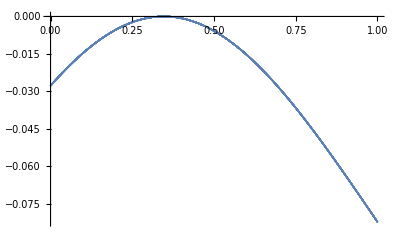

```mathematica
(* {genotypes,genotypeabundances}=getRandomFitDistr[popsize,{10,50},{10,20},0]; *)
(* {genotypes,genotypeabundances}=getInitial2Ddistribution[5,popsize,Δc1,Δc2,U1,U2]; *)
genotypes={{2,1},{1,2},{3,2},{2,3}}
genotypeabundances=popsize {1/3,1/3,1/6,1/6}
covt={};
result=myCovDSelectionTest[popsize,Δc1,Δc2,genotypes,genotypeabundances,maxtime,timestep];
Do[
covt=Join[covt,{{result[[i]][[1]],result[[i]][[2]]}}];
,{i,1,Length[result]}];
ListPlot[covt,PlotRange->All]
```

{{2,1},{1,2},{3,2},{2,3}}

{2500000,2500000,2500000,2500000}

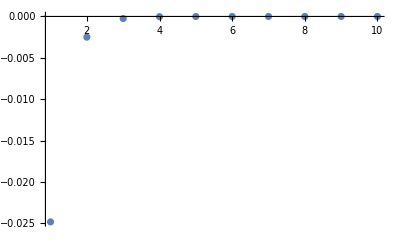

{{1,-0.0248343},{2,-0.00249983},{3,-0.00025},{4,-0.000025},{5,-2.5×10^-6},{6,-2.5×10^-7},{7,-2.5×10^-8},{8,-2.5×10^-9},{9,-2.5×10^-10},{10,-2.5×10^-11}}

```mathematica
dcovdt={};
genotypes={{2,1},{1,2},{3,2},{2,3}}
genotypeabundances=popsize {1/4,1/4,1/4,1/4}
Do[
result=myCovDSelectionTest[popsize,Δc1,Δc2,genotypes,genotypeabundances,10^-i,10^-i];
dcovdt=Join[dcovdt,{{i,(result[[-1]][[2]])/(result[[-1]][[1]])}}];
,{i,1,10}];
ListPlot[dcovdt,PlotRange->All]
dcovdt
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{4,1},{4,2},{5,1}},{665799.,143442.,6657.99,66.5799,0.143442,143442.,30903.6,1434.42,14.3442,6657.99,1434.42,66.5799,66.5799,14.3442,0.143442}}

15

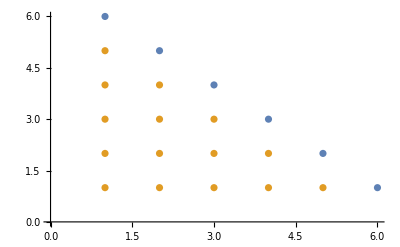

```mathematica
(* Testing Code for linkage disequilibria matrix *)
{Δc1,Δc2,U1,U2,popsize}={10.0^-2,10.0^-2,10.0^-4,10.0^-4,10.0^6};
{starttime,timestep,maxtime}={0,1000,25000000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[5,popsize,Δc1,Δc2,U1,U2]
numbgenotypes=Length[genotypes]
ListPlot[{Complement[ParallelTable[genotypes[[Mod[i,numbgenotypes,1]]]+{Round[1-(i-1)/(2numbgenotypes)],Round[i/(2numbgenotypes)]},{i,1,2 numbgenotypes}],genotypes],genotypes}]
```

```mathematica
AbsoluteTiming[getNextMutants[genotypes,genotypeabundances,Δc1,Δc2]]
```

{0.00078,{{{2,5},{{5,1},{9,2}},0,0},{{3,4},{{9,1},{12,2}},0,0},{{4,3},{{12,1},{14,2}},0,0},{{5,2},{{14,1},{15,2}},0,0},{{6,1},{{15,1}},0,0},{{1,6},{{5,2}},0,0}}}

```mathematica
Complement[{a,a,b,c,d},{b,c}]
```

{a,d}

```mathematica
AbsoluteTiming[Table[i,{i,1,10}]]
```

{5.×10^-6,{1,2,3,4,5,6,7,8,9,10}}